{x→-0.0948936}

{x→0.104615}

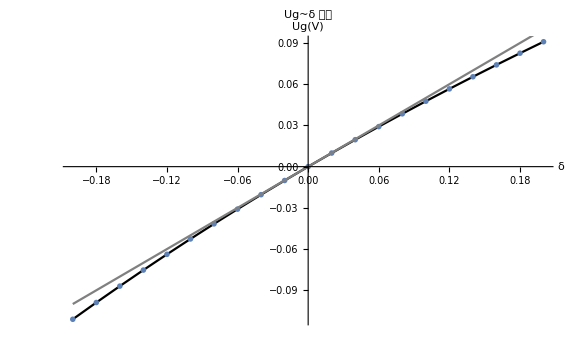

```mathematica
(* Exp1 *)
r4 = Range[800,1200,20];
ug = {-111.09,-98.89,-86.95,-75.26,-63.82,-52.62,-41.65,-30.92,-20.40,-10.09,0,9.90,19.61,29.13,38.46,47.62,56.60,65.42,74.08,82.57,90.91} * 10^-3;
us = 2.0;
r0 = r1 = r2 = 1000;
r3 = 999.72;
deltar = r4 - r0;
ith = (r4 - r0) / r0;

data1 = Transpose[{ith, ug}];
data2y[x_] := us * x / 4;
grah = Interpolation[data1,InterpolationOrder->1];

FindRoot[Abs[data2y[x] - grah[x]] - Abs[0.05 * data2y[x]] ,{x,-0.2}]
FindRoot[Abs[data2y[x] - grah[x]] - Abs[0.05 * data2y[x]] ,{x,0.2}]
tmpx = 0.10461538461538444;
Abs[data2y[tmpx] - grah[tmpx]] - Abs[0.05 * data2y[tmpx]];
tmpx = -0.09489361702127669;
Abs[data2y[tmpx] - grah[tmpx]] - Abs[0.05 * data2y[tmpx]];

Show[Plot[grah[x],{x,Min[ith],Max[ith]},PlotStyle->Black],
ListPlot[data1,PlotMarkers->Style["x",10]],
Plot[data2y[x], {x,Min[ith],Max[ith]},PlotStyle->Gray],
AxesLabel->{Style["δ",10], Style["Ug(V)",9]},
PlotLabel->Style["Ug~δ 曲线",25,FontFamily->"Hack",Bold,FontColor->Black],
ImageSize->Large]
```

```mathematica
(* Exp2 - 1 *)
```

{x→-0.0949436}

{x→0.10536}

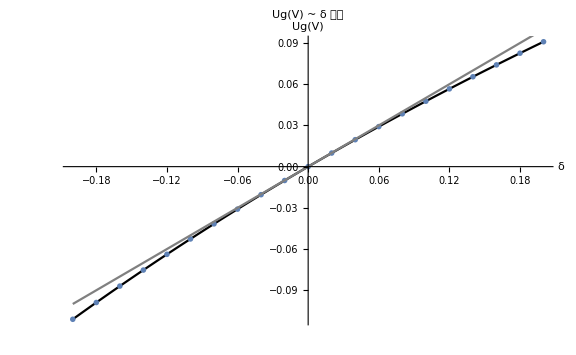

0.499917

2499.58

```mathematica
r0 = 5000;
r1 = r2 = r0;
r3 = 4999.18;
r4 = Range[4000,6000,100];
ug = {-111.12,-98.91,-86.96,-75.28,-63.83,-52.64,-41.67,-30.93,-20.41,-10.10,0,9.90,19.61,29.13,38.46,47.62,56.61,65.43,74.08,82.58,90.92} * 10^-3;
deltar = r4 - r0;
ith = deltar / r0;

data1 = Transpose[{ith, ug}];
data2y[x_] := us * x / 4;
grah = Interpolation[data1];

FindRoot[Abs[data2y[x] - grah[x]] - Abs[0.05 * data2y[x]] ,{x,-0.2}]
FindRoot[Abs[data2y[x] - grah[x]] - Abs[0.05 * data2y[x]] ,{x,0.2}]
tmpx = 0.10461538461538444;
Abs[data2y[tmpx] - grah[tmpx]] - Abs[0.05 * data2y[tmpx]];
tmpx = -0.09489361702127669;
Abs[data2y[tmpx] - grah[tmpx]] - Abs[0.05 * data2y[tmpx]];

gra1 = Show[Plot[grah[x],{x,Min[ith],Max[ith]},PlotStyle->Black],
ListPlot[data1,PlotMarkers->Style["x",10]],
Plot[data2y[x], {x,Min[ith],Max[ith]},PlotStyle->Gray],
AxesLabel->{Style["δ",10], Style["Ug(V)",9]},
PlotLabel->Style["Ug(V) ~ δ 曲线",25,FontFamily->"Hack",Bold,FontColor->Black],
ImageSize->Large]
D[grah[x],x]/.x->0
D[grah[x] * r0,x]/.x->0
```

```mathematica
(* Exp 2-2 *)
```

{x→-0.0992955}

{x→0.105147}

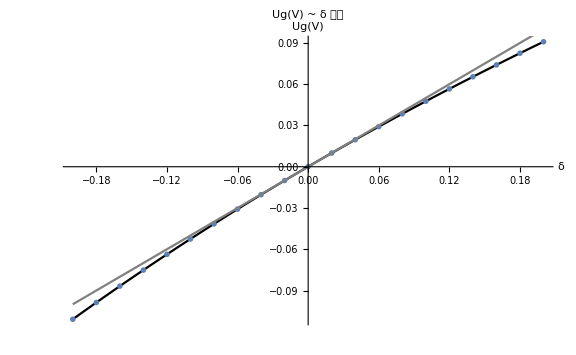

0.499583

24.9792

```mathematica
r0 = 50;
r1 = r2 = r0;
r3 = 499.90;
r4 = Range[40,60,1];
ug = {-110.90,-98.72,-86.79,-75.12,-63.70,-52.52,-41.56, -30.83,-20.32,-10.03,0.07,9.94,19.64,29.14,38.47,47.62,56.59,65.40,74.05,82.54,90.87} * 10^-3;
deltar = r4 - r0;
ith = deltar / r0;

data1 = Transpose[{ith, ug}];
data2y[x_] := us * x / 4;
grah = Interpolation[data1];

FindRoot[Abs[data2y[x] - grah[x]] - Abs[0.05 * data2y[x]] ,{x,-0.2}]
FindRoot[Abs[data2y[x] - grah[x]] - Abs[0.05 * data2y[x]] ,{x,0.2}]
tmpx = 0.10461538461538444;
Abs[data2y[tmpx] - grah[tmpx]] - Abs[0.05 * data2y[tmpx]];
tmpx = -0.09489361702127669;
Abs[data2y[tmpx] - grah[tmpx]] - Abs[0.05 * data2y[tmpx]];

gra2 = Show[Plot[grah[x],{x,Min[ith],Max[ith]},PlotStyle->Black],
ListPlot[data1,PlotMarkers->Style["x",10]],
Plot[data2y[x], {x,Min[ith],Max[ith]},PlotStyle->Gray],
AxesLabel->{Style["δ",10], Style["Ug(V)",9]},
PlotLabel->Style["Ug(V) ~ δ 曲线",20,FontFamily->"Hack",Bold,FontColor->Black],
ImageSize->Large]
D[grah[x],x]/.x->0
D[grah[x] * r0,x]/.x->0
```

{{27,0.237},{30,0.24},{35,0.245},{40,0.25},{45,0.255},{50,0.26},{55,0.264},{60,0.269},{65,0.274},{70,0.279},{75,0.284},{80,0.289},{85,0.294}}

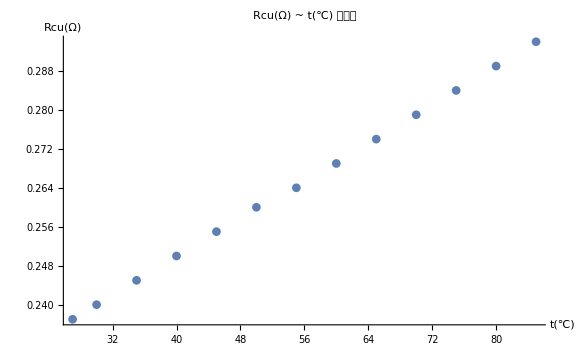

```mathematica
r0 = 50;
us = 2.0;
ug = {2.37, 2.40, 2.45, 2.50, 2.55, 2.60, 2.64, 2.69, 2.74, 2.79, 2.84, 2.89,2.94} * 10^-3;
t = Join[{27},Range[30,85,5]];
deltar = ug * 4 * r0 / us;
rcu = deltar;
cudata = Transpose[{t,rcu}]

(* Point Graph *)
gra3 = Show[ListPlot[cudata, PlotMarkers->Automatic],
PlotLabel->Style["Rcu(Ω) ~ t(℃) 散点图",20,FontFamily->"Hack",FontColor->Black,FontWeight->Bold],
AxesLabel->{Style["t(℃)",10],Style["Rcu(Ω)",10]},
ImageSize->Large]
```

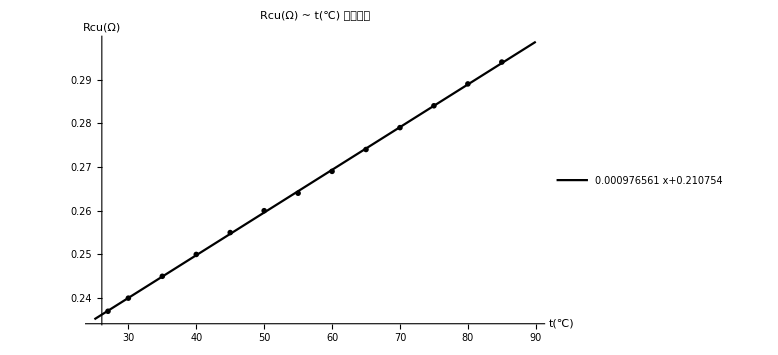

```mathematica
(* Fitting Plot *)
nlm = LinearModelFit[cudata,x,x];
tab = nlm["ParameterTable"];

fitA = Fit[cudata,{1,x},x];
gra4 = Show[ListPlot[cudata,PlotStyle->Black,PlotMarkers->Style["x",10]],
Plot[fitA,{x,25,90},PlotStyle->Black,PlotLegends->{Placed[LineLegend[{Black},{Style[Normal[nlm],9,Bold]},LegendMarkerSize->{40,1},
LegendFunction->(Column[{#,tab},Frame->True]&)],{0.35,0.8}]}],
AxesLabel->{Style["t(℃)",10],Style["Rcu(Ω)",10]},
PlotLabel->Style["Rcu(Ω) ~ t(℃) 拟合曲线",20,FontFamily->"Hack",FontColor->Black,FontWeight->Bold],
PlotRange->All,
ImageSize->Large]
```

```mathematica
Export["~/tmp/1.jpg",gra1,ImageResolution->1000]
Export["~/tmp/2.jpg",gra2,ImageResolution->1000]
Export["~/tmp/3.jpg",gra3,ImageResolution->1000]
Export["~/tmp/4.jpg",gra4,ImageResolution->1000]
```

~/tmp/1.jpg

~/tmp/2.jpg

~/tmp/3.jpg

~/tmp/4.jpg